```mathematica
(* Given coordinates (x, y), generates new coordinates resulting from rotation by angle T *)
rotateSphere[x_,y_,T_]:=N[{Cos[T]*x-Sin[T]*y,Sin[T]*x+Cos[T]*y}];
```

```mathematica
computeX[a_,b_]:=a+Sqrt[4-b^2];
```

```mathematica
(* Initial list of paticles *)
particles={{0,0},{Sqrt[2],Sqrt[2]}};
For[i=1,i<1000,i++;
(* Generate a random angle *)
T=2*Pi*Random[];
(* Rotate entire system in reference frame of T *)
particles=rotateSphere[#[[1]],#[[2]],T]&/@particles;
possibleParticles=Select[particles,Abs[#[[2]]]<2&&#[[1]]≥0&];
newX=Max[computeX[#[[1]],#[[2]]]&/@possibleParticles];
particles=Append[particles,{newX,0}];]
```

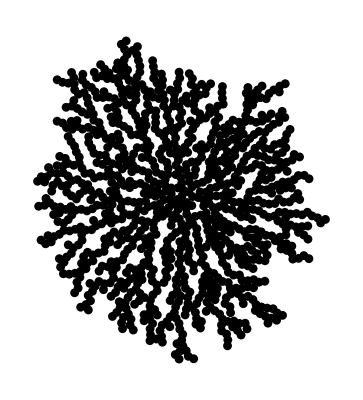

```mathematica
Graphics[{Disk[#, 1.5]&/@particles}]
```

```mathematica
(* Initial list of paticles *)
L=300;
particles={2*#, 0}&/@Range[L/2];
For[i=1,i<10000,i++;
(* Generate a random angle *)
T=L*Random[];
possibleParticles=Select[particles,Abs[(#[[1]]-T)]<2&];
newY=Max[computeX[#[[2]], #[[1]]-T]&/@possibleParticles];
particles=Append[particles,{T,newY}];]
```

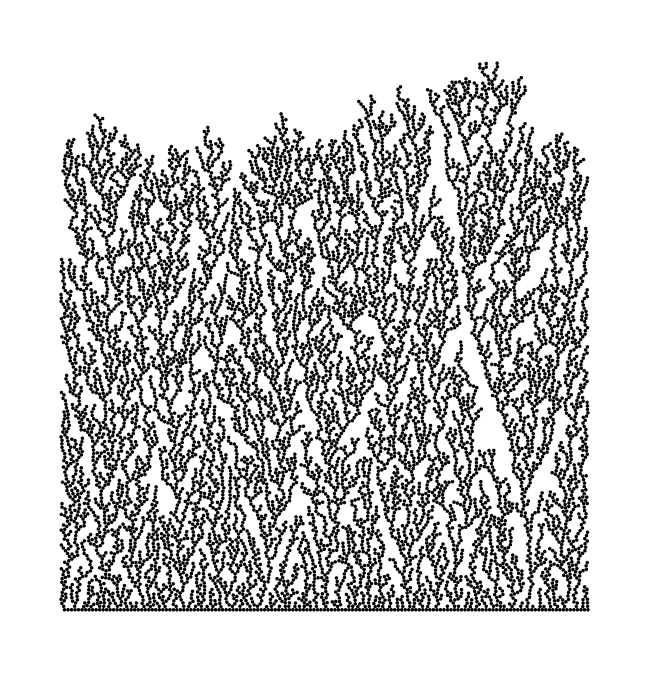

```mathematica
Graphics[{Disk[#, 1]&/@particles}]
```

```mathematica
Max[#[[2]]&/@particles]
```

311.146

```mathematica
density[q_]:=N[Pi*Length[Select[particles, #[[2]]< q&]]/(300*2*q)]/N[Pi/4]
```

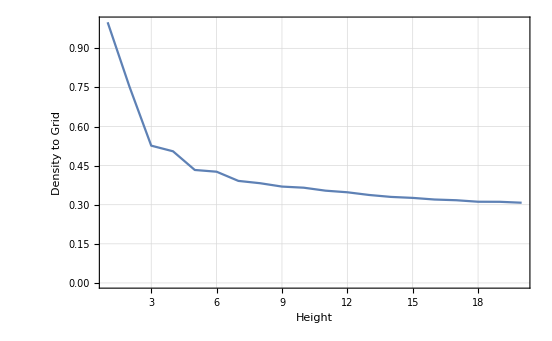

```mathematica
ListPlot[{#, density[#]}&/@Range[20], Joined->True, PlotRange->All, Frame->True, FrameLabel->{ "Height", "Density to Grid"}, GridLines->Automatic, FrameStyle->Directive[14] ]
```

```mathematica
ListPlot[%, PlotRange->All]
```

Union::normal: Nonatomic expression expected at position 1 in Union[Null].

ListPlot::lpn: Null is not a list of numbers or pairs of numbers.

Union::normal: Nonatomic expression expected at position 1 in Union[Null].

General::stop: Further output of Union :: normal will be suppressed during this calculation.

ListPlot::lpn: Null is not a list of numbers or pairs of numbers.

ListPlot[Null,PlotRange→All]

```mathematica
Pi*Length[Select[particles, #[[2]]< 1 &]]/
```

```mathematica
particles[[150]]
```

{300,0}

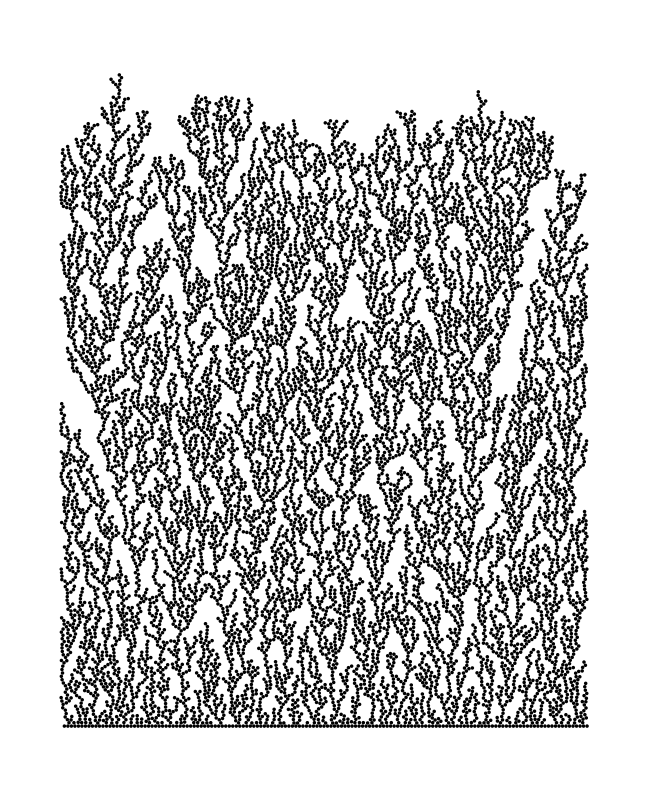

```mathematica
Graphics[{Disk[#, 1]&/@particles}]
```

```mathematica
Length[particles]
```

10149

```mathematica
computeThing[x_]:={x, Length[Select[particles, #[[2]]< x &]]}
```

```mathematica
Max[#[[2]]&/@particles]
```

371.7

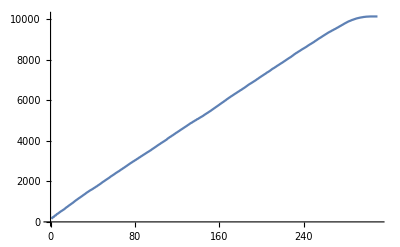

```mathematica
ListPlot[computeThing[#]&/@Range[310], Joined->True]
```

```mathematica
For[i=1,i<4000,i++;
(* Generate a random angle *)
T=L*Random[];
possibleParticles=Select[particles,Abs[(#[[1]]-T)]<2 && #[[2]]>200 &];
newY=Max[computeX[#[[2]], #[[1]]-T]&/@possibleParticles];
particles=Append[particles,{T,newY}];]
```

```mathematica
ArcSin[Sqrt[3]/2]
```

π/3